```mathematica
t[n_,k_]:=Length@IntegerPartitions[n,k];Table[t[n,k],{n,12},{k,n}]//Flatten

(*Second program:*)

T[n_,k_]:=T[n,k]=If[n==0||k==1,1,T[n,k-1]+If[k>n,0,T[n-k,k]]];Table[T[n,k],{n,1,12},{k,1,n}]//Flatten
```

{1,1,2,1,2,3,1,3,4,5,1,3,5,6,7,1,4,7,9,10,11,1,4,8,11,13,14,15,1,5,10,15,18,20,21,22,1,5,12,18,23,26,28,29,30,1,6,14,23,30,35,38,40,41,42,1,6,16,27,37,44,49,52,54,55,56,1,7,19,34,47,58,65,70,73,75,76,77}

{1,1,2,1,2,3,1,3,4,5,1,3,5,6,7,1,4,7,9,10,11,1,4,8,11,13,14,15,1,5,10,15,18,20,21,22,1,5,12,18,23,26,28,29,30,1,6,14,23,30,35,38,40,41,42,1,6,16,27,37,44,49,52,54,55,56,1,7,19,34,47,58,65,70,73,75,76,77}

```mathematica
Table[{k,Length@IntegerPartitions[k,{4}]},{k,4,10}]//MatrixForm
```

(4 | 1
5 | 1
6 | 2
7 | 3
8 | 5
9 | 6
10 | 9)

```mathematica
IntegerPartitions[6,{4}]
```

{{3,1,1,1},{2,2,1,1}}

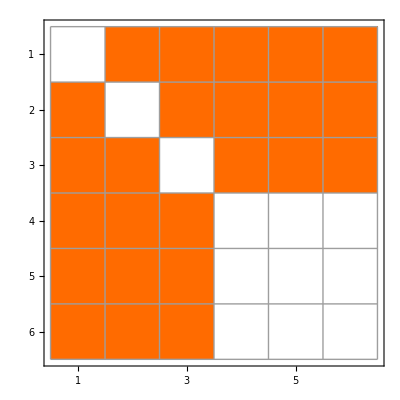
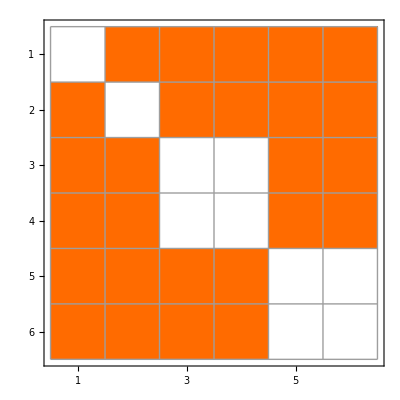
-Graphics---1113 | -Graphics---1122

```mathematica
Map[Labeled[MatrixPlot[AdjacencyMatrix[#], Mesh->True],Framed[Style[Row[Map[Length,SymbolToSets[First[FindFullFormula4[#]]]],"-"],{"Tahoma",8,Darker[Green]}]]]&,BarelyFourColorableGraphsOfCount[6]]//Multicolumn
```

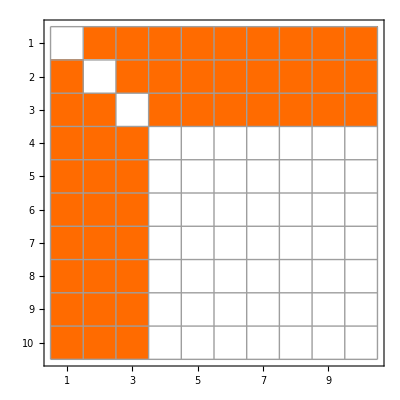
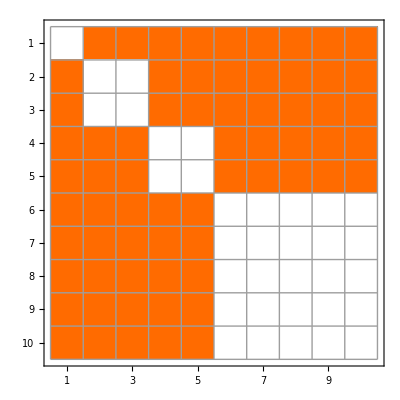
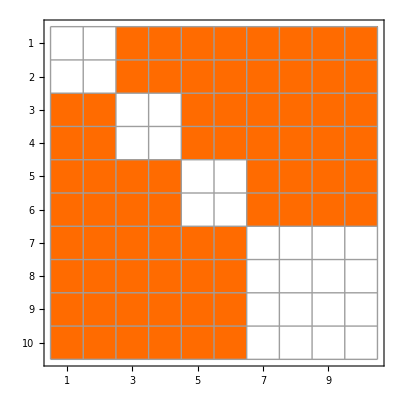
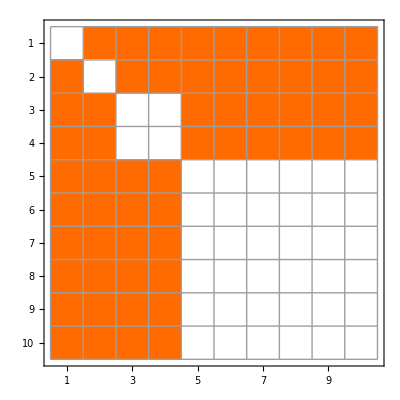
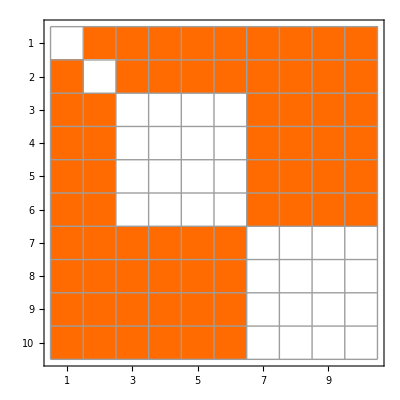
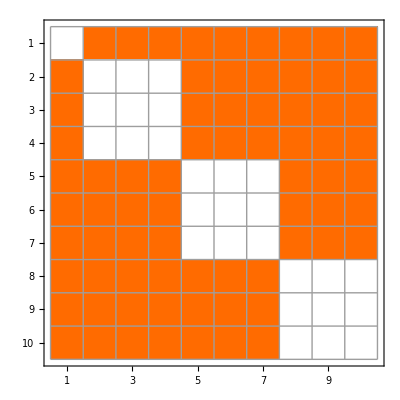
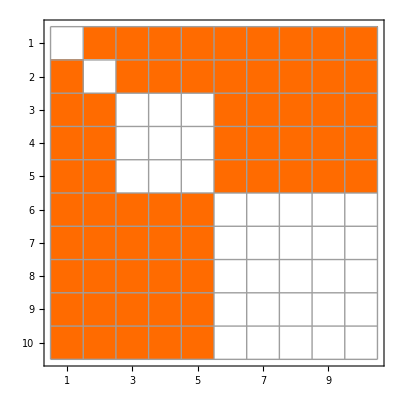
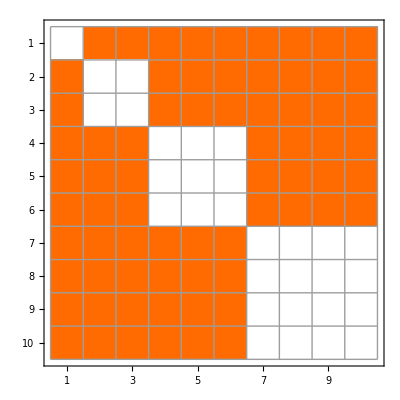
-Graphics---1117→24 | -Graphics---1225→33 | -Graphics---2224→36
-Graphics---1126→29 | -Graphics---1144→33 | -Graphics---1333→36
-Graphics---1135→32 | -Graphics---1234→35 | -Graphics---2233→37

```mathematica
Map[Labeled[MatrixPlot[AdjacencyMatrix[#], Mesh->True],Framed[Style[Row[Map[Length,SymbolToSets[First[FindFullFormula4[#]]]],"-"],{"Tahoma",8,Darker[Green]}]]->EdgeCount[#]]&,BarelyFourColorableGraphsOfCount[10]]//Multicolumn
```

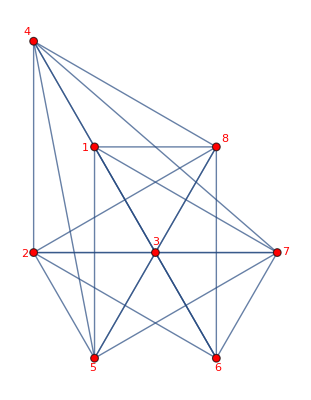
```mathematica
Map[ToColors2[SymbolToSets[#]]&,FindFullFormula4[-Graphics-]]
```

{{1→RGBColor[1, 0, 0],2→RGBColor[1, 0, 0],3→RGBColor[0, 1, 0],4→RGBColor[0, 1, 0],5→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],7→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0]}}

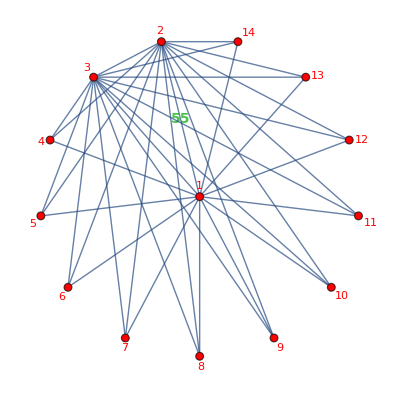
```mathematica
MatrixPlot[AdjacencyMatrix[-Graphics-], Mesh->True]
```

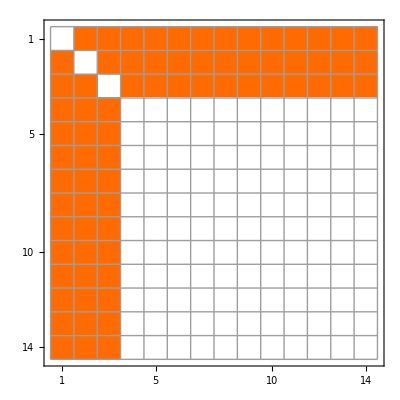

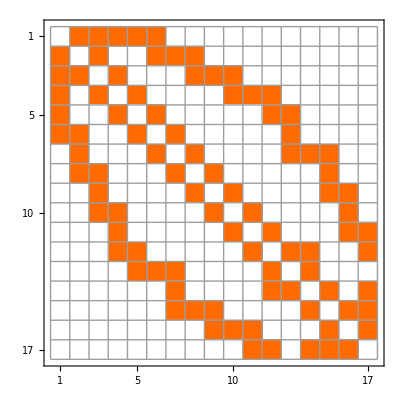

```mathematica
MatrixPlot[AdjacencyMatrix[plantri8], Mesh->True]
```

```mathematica
FindFullFormula4[plantri8]
```

{v14acx29bdx357hx68efg,v14acx259dx37bhx68efg,v137gx24acx568fx9bdeh,v14acx259dfx37ghx68be,v14acx259dfx37bhx68eg,v14adx29bcx357hx68efg,v14adx259cx37bhx68efg,v137gx258acx4bdhx69ef,v137gx258acx46fx9bdeh,v1467x258acx3fgx9bdeh,v1467x258acx39bhxdefg,v146ax259dfx37ghx8bce,v146ax259dfx37bhx8ceg,v139cx25adx47bhx68efg,v13acx259dx47bhx68efg,v13acx247bx59dhx68efg,v139cx247bx5adhx68efg,v1467x28fgx35acx9bdeh,v13cgx259dfx467bx8aeh,v13acx259dfx467bx8egh,v13cgx259dfx47bhx68ae,v13acx259dfx47bhx68eg}

```mathematica
Repermute[l_]:=Block[{result=Association[],i},
For[i=1,i<=Length[l],i++,
Print[i, "     ", l[[i]]];
result[i]=l[[i]]
];
Print[result];
result
]
```

```mathematica
(SymbolToSets[v14acx29bdx357hx68efg]//Flatten)[[1]]
```

1

```mathematica
MyPermute[g_,symbol_]:=Block[{result, swaps, swop=Association[], pos,sets, offset=0},
sets=SymbolToSets[symbol];
swaps=Flatten[sets];
result=Table[0,{i,Length[swaps]},{j,Length[swaps]}];
For[pos=1,pos<=Length[swaps],pos++,
swop[swaps[[pos]]]=pos;
];
Table[
result[[swop[edge[[1]]],swop[edge[[2]]]]]=1;
result[[swop[edge[[2]]],swop[edge[[1]]]]]=1;
,{edge,EdgeList[g]}
];
Table[
Table[result[[offset+i,offset+j]]=-1,{i,1,Length[s]},{j,1,Length[s]}];
offset+=Length[s]
,{s,sets}];
result
]
```

```mathematica
Table[sol->Length[Select[Flatten[MyPermute[GraphComplement[plantri8],sol]],#==0&]],
{sol,FindFullFormula4[plantri8]}]
```

{v14acx29bdx357hx68efg→90,v14acx259dx37bhx68efg→90,v137gx24acx568fx9bdeh→90,v14acx259dfx37ghx68be→90,v14acx259dfx37bhx68eg→90,v14adx29bcx357hx68efg→90,v14adx259cx37bhx68efg→90,v137gx258acx4bdhx69ef→90,v137gx258acx46fx9bdeh→90,v1467x258acx3fgx9bdeh→90,v1467x258acx39bhxdefg→90,v146ax259dfx37ghx8bce→90,v146ax259dfx37bhx8ceg→90,v139cx25adx47bhx68efg→90,v13acx259dx47bhx68efg→90,v13acx247bx59dhx68efg→90,v139cx247bx5adhx68efg→90,v1467x28fgx35acx9bdeh→90,v13cgx259dfx467bx8aeh→90,v13acx259dfx467bx8egh→90,v13cgx259dfx47bhx68ae→90,v13acx259dfx47bhx68eg→90}

```mathematica
Monitor[Table[k->With[{g=Graph[plantri[[k]]]},
With[{sol=First[FindFullFormula4[g]]},
sol->With[
{
edges=EdgeCount[g],
zeroes=Length[Select[Flatten[MyPermute[g,sol]],#==0&]]
},
{edges,zeroes, zeroes/2}]
]],{k,1,3}],k]
```

{1→v19bx25cx37ax468→{30,48,24},2→v1ex25adx368bx479c→{36,72,36},3→v1dfx25aex368bx479c→{39,90,45}}

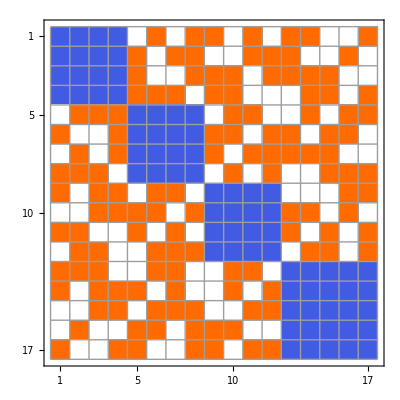
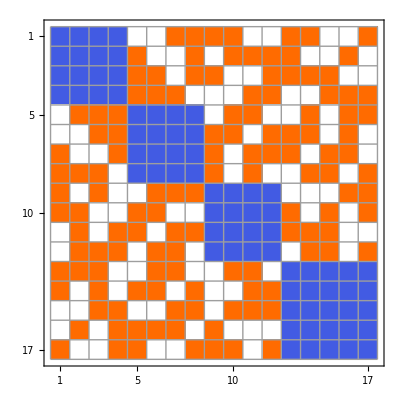
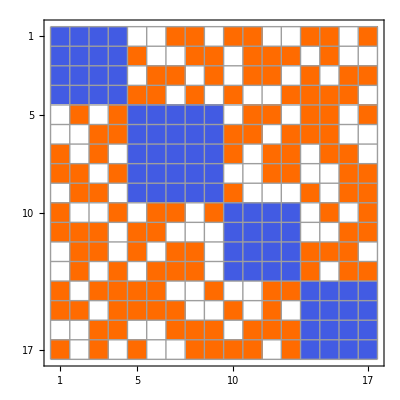
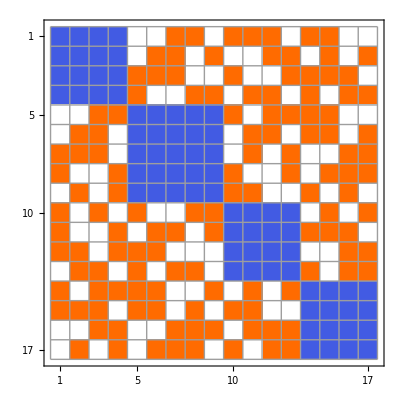
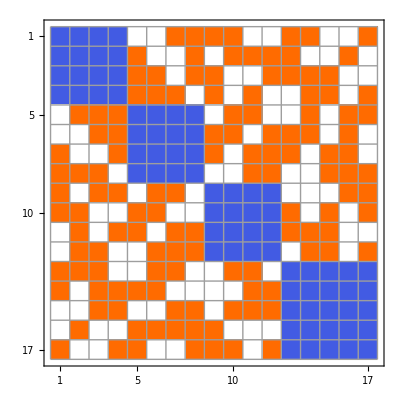
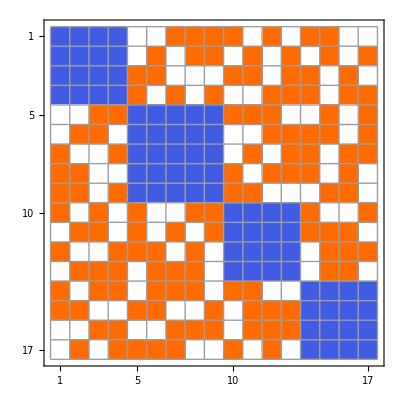
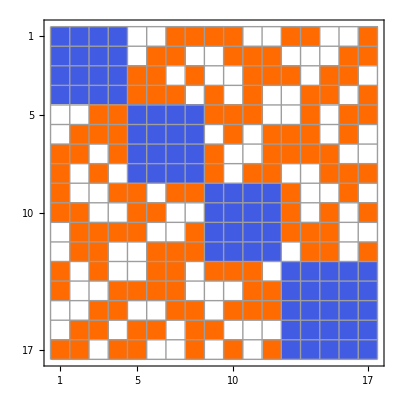
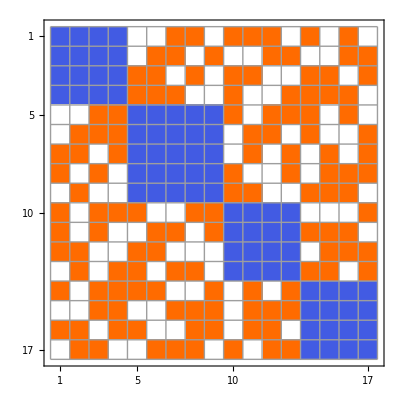
-Graphics-14ac♁29bd♁357h♁68efg | -Graphics-14ad♁259c♁37bh♁68efg | -Graphics-146a♁259df♁37bh♁8ceg | -Graphics-13cg♁259df♁467b♁8aeh
-Graphics-14ac♁259d♁37bh♁68efg | -Graphics-137g♁258ac♁4bdh♁69ef | -Graphics-139c♁25ad♁47bh♁68efg | -Graphics-13ac♁259df♁467b♁8egh
-Graphics-137g♁24ac♁568f♁9bdeh | -Graphics-137g♁258ac♁46f♁9bdeh | -Graphics-13ac♁259d♁47bh♁68efg | -Graphics-13cg♁259df♁47bh♁68ae
-Graphics-14ac♁259df♁37gh♁68be | -Graphics-1467♁258ac♁3fg♁9bdeh | -Graphics-13ac♁247b♁59dh♁68efg | -Graphics-13ac♁259df♁47bh♁68eg
-Graphics-14ac♁259df♁37bh♁68eg | -Graphics-1467♁258ac♁39bh♁defg | -Graphics-139c♁247b♁5adh♁68efg | 
-Graphics-14ad♁29bc♁357h♁68efg | -Graphics-146a♁259df♁37gh♁8bce | -Graphics-1467♁28fg♁35ac♁9bdeh |

```mathematica
Multicolumn[Table[Labeled[MatrixPlot[MyPermute[GraphComplement[plantri8],sol],Mesh->True],SymbolToLabel[sol]],
{sol,FindFullFormula4[plantri8]}],4]
```

```mathematica
m=AdjacencyMatrix[plantri8];
```

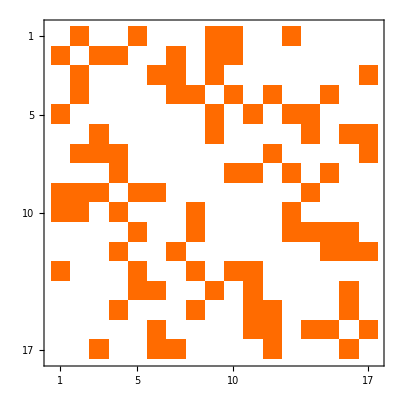

```mathematica
m[[{1,4,10,12,2,9,11,13,3,5,7,17,6,8,14,15,16},{1,4,10,12,2,9,11,13,3,5,7,17,6,8,14,15,16}]]//MatrixPlot
```

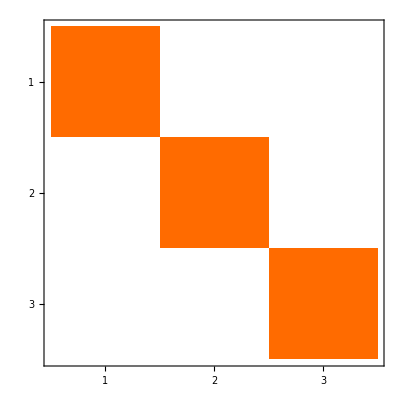

```mathematica
m=IdentityMatrix[3]//MatrixPlot
```

```mathematica
m[[{3,2,1},{3,2,1}]]//MatrixPlot
```

Part::partw: Part {3,2,1} of FrameLabel→{None,None} does not exist.

MatrixPlot::mat0: Argument ()⟦{3,2,1},{3,2,1}⟧ at position 1 is not a matrix.

MatrixPlot[(-Graphics-)⟦{3,2,1},{3,2,1}⟧]